## Functions

```mathematica
Py[ex_]:=ExportString[ex,"PythonExpression"]
```

```mathematica
ArrToStrPyOld[arr_]:="["<>StringTrim@StringJoin[", "<>ToString[#,InputForm]&/@arr]<>"]";
```

```mathematica
ArrToStrPy[arr_]:="["<>StringJoin[Table[ToString[arr⟦n⟧]<>If[n<Length[arr],", ",""],{n,1,Length[arr]}]]<>"]";
```

```mathematica
ArrToStrPy2[paramDiv]
```

ArrToStrPy2[paramDiv]

```mathematica
StringJoin[ToString[#]&/@paramDiv]
```

StringJoin::string: String expected at position 1 in StringJoin[paramDiv].

StringJoin[paramDiv]

## Environment setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules

```mathematica
texStyle={FontFamily->"Times New Roman",FontSize->14,FontWeight-> "Plain"};
```

```mathematica
<<MaTeX`
```

## Python start session

```mathematica
sessPy=StartExternalSession["Python"];
```

```mathematica
ExternalEvaluate[sessPy, "sys.path.insert(1, '')"];
```

```mathematica
ExternalEvaluate[sessPy,"import numpy as np"];
```

## Variables

```mathematica
Mlst={10};
paramDiv={80,16,16};
dim=3;
instanceNum=5000;
seed=1000;
```

```mathematica
isDistilled=True;
```

```mathematica
If[isDistilled, 
fileNameMain="deltaN_distill";
fileNameFfuncMain="ffunc_distilled_dim_3";
fileNameGMain="gDistilled_dim_3";
mMaxSh=1;xyLabs=MaTeX[#,Magnification->1]&/@{"\\chi / 2\\pi","\\langle \\left( \\Delta S_m \\right)^2 \\rangle"};
yLabRot=0,
fileNameMain="deltaN";
fileNameGMain="gLst";
fileNameFfuncMain="ffunc";
mMaxSh=0;
xyLabs=MaTeX[#,Magnification->1]&/@{"\\chi / 2\\pi","\\langle \\left( \\Delta C_n \\right)^2 \\rangle"};
(*yLabRot=-90Degree;*)
yLabRot=0;
]
```

0

```mathematica
xyLabs
```

{-Graphics-,-Graphics-}

```mathematica
(*fileNameMain="deltaN";*)
```

```mathematica
div=paramDiv⟦1⟧;
xCoords=1/div Table[x,{x,0,div}];
```

```mathematica
nameAppend[arr_,app_]:=arr<>"_"<>app;
```

```mathematica
ArrToStrPy[paramDim]
```

[]

```mathematica
\\-\
```

```mathematica
npyType=".npy";
jpgType=".jpg";
```

```mathematica
fileNameMod="degObj";
fileNameMod="";
fileNameModOut="";
```

```mathematica
Length[Mlst]
```

1

```mathematica
xyLabs=MaTeX[#,Magnification->1.0]&/@{"\\frac{k_3}{2\\pi}","\\Delta C^2"};
```

```mathematica
(*xyLabs=MaTeX[#,Magnification->1.0]&/@{"k_3 / 2\\pi","\\langle \\Delta C^2 \\rangle"};*)
```

```mathematica
xyLabs=MaTeX[#,Magnification->1.0]&/@{"\\chi / 2\\pi","\\langle \\Delta C^2 \\rangle"};
```

```mathematica
xyLabs
```

{-Graphics-,-Graphics-}

```mathematica
fileName
```

fileName

```mathematica
xyLabs
```

{-Graphics-,-Graphics-}

```mathematica
dataLab=MaTeX[#,Magnification->0.8]&/@{"\\mathrm{data}"};
uncorrLab=MaTeX[#,Magnification->0.8]&/@{"\\mathrm{uncorrelated}"};
```

```mathematica
fileNameGlst
```

gLst_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000.npy

## Plotting

```mathematica
legX=0.22;
legLn=18;
```

```mathematica
{{True,False},{True,False}}
```

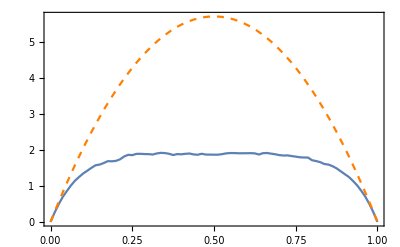

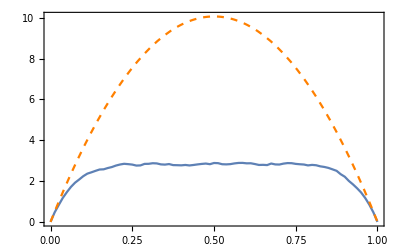

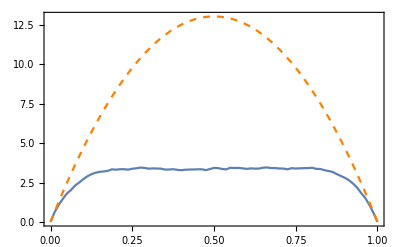

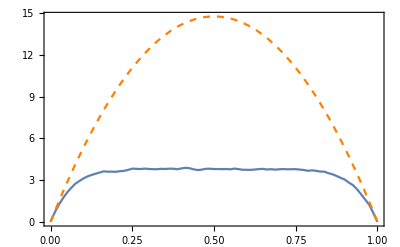

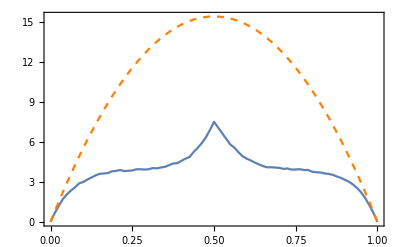

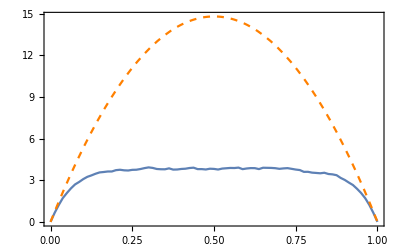

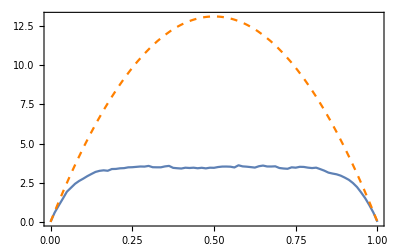

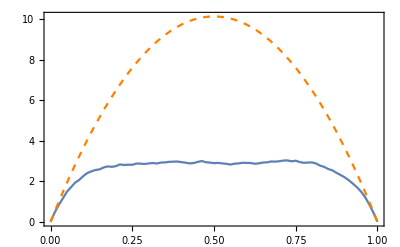

```mathematica
For[itM=1,itM≤Length[Mlst],itM++,
 M=Mlst⟦itM⟧;
fileNameAttrPre="_N_" <>ToString[M];
fileNameAttrFull=fileNameAttrPre;
fileNameAttr=fileNameAttrPre<>"_param_divide_"<>ArrToStrPy[paramDiv]<>"_instanceNum_"<>ToString[instanceNum]<>"_seed_"<>ToString[seed];
fileName=fileNameMain<>fileNameAttr;
fileNameGlst=fileNameGMain<>fileNameAttr;
If[fileNameMod≠"",
fileName=nameAppend[fileName,fileNameMod];
fileNameGlst=nameAppend[fileNameGlst,fileNameMod];];
fileName=fileName<>npyType;
fileNameGlst=fileNameGlst<>npyType;
deltaNLst=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileName]<>")"]];
gLstRaw=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileNameGlst]<>")"]];
gLst=gLstRaw⟦1⟧;
For[m=1,m≤M-mMaxSh,m++,
yy={deltaNLst⟦m,-1⟧}~Join~deltaNLst⟦m⟧;
title=MaTeX["M = "<>ToString[M]<>", m = "<>ToString[m],Magnification->1.1];
datPlot=ListLinePlot[Transpose@{xCoords,yy},PlotLegends->Placed[LineLegend[dataLab,LegendMarkerSize->18],{{legX,0.53},Right}],PlotRange->All];
uncorrPlot=Plot[2gLst⟦m⟧x(1-x),{x,0,1},PlotStyle->{Orange,Dashed},PlotLegends->Placed[LineLegend[uncorrLab,LegendMarkerSize->18],{{legX,0.43},Right}]];
(*xyLabs=MaTeX/@{"\\frac{k_z}{2\\pi}","\\Delta C^2"};*)
Print[Show[datPlot,uncorrPlot,BaseStyle->texStyle,PlotLabel->title,PlotRange-> All,PlotRangePadding->{None,{None,Scaled[0.05]}},FrameLabel->{xyLabs⟦1⟧,Rotate[xyLabs⟦2⟧,yLabRot]},Frame->True,ImageSize->{Automatic,6 cm}]];
]
]
```

```mathematica
{None,{None,Scaled[0.05]}}
```

```mathematica
m=4;
yMax=15;
yStep=5;
yDiv=yMax/yStep;
```

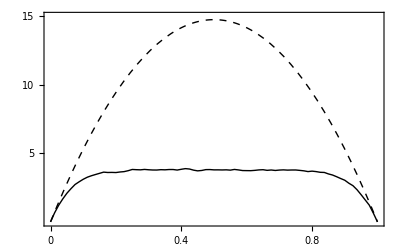

```mathematica
yy={deltaNLst⟦m,-1⟧}~Join~deltaNLst⟦m⟧;
title=MaTeX["M = "<>ToString[M]<>", m = "<>ToString[m],Magnification->1.1];
datPlot=ListLinePlot[Transpose@{xCoords,yy},PlotStyle->{Black,dataThick},PlotLegends->Placed[LineLegend[dataLab,LegendMarkerSize->legMkSz],{{legX,0.53},Right}],PlotRange->All];
uncorrPlot=Plot[2gLst⟦m⟧x(1-x),{x,0,1},PlotStyle->{Black,Dashed,dataThick},PlotLegends->Placed[LineLegend[uncorrLab,LegendMarkerSize->legMkSz],{{legX,0.43},Right}]];
(*xyLabs=MaTeX/@{"\\frac{k_z}{2\\pi}","\\Delta C^2"};*)
Print[Show[datPlot,uncorrPlot,Graphics[Text[capTex⟦2⟧,Scaled[{0.1,0.85}]]],BaseStyle->texStyle,PlotLabel->None,PlotRange-> {All,{0,yMax}},FrameTicks->{{Charting`ScaledTicks["Linear"][0.5,yMax,{yDiv,5}],None},{Charting`ScaledTicks["Linear"][0,1,{5,4}],None}},PlotRangePadding->None,FrameLabel->{xyLabs⟦1⟧,Rotate[xyLabs⟦2⟧,yLabRot]},Frame->True,ImageSize->{Automatic,6 cm}]];
```

```mathematica
Table[a,{a,0,15,5}]
```

{0,5,10,15}

```mathematica
yy={deltaNLst⟦m,-1⟧}~Join~deltaNLst⟦m⟧;
```

```mathematica
datPlot=ListLinePlot[Transpose@{xCoords,yy2},PlotLegends->Placed[LineLegend[dataLab],{0.47,0.4}],PlotRange->All];
```

Transpose::nmtx: The first two levels of {{0,1/80,1/40,3/80,1/20,1/16,3/40,7/80,1/10,9/80,«71»},yy2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.0125,0.025,0.0375,0.05,0.0625,0.075,0.0875,0.1,0.1125,«71»},yy2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0125,0.025,0.0375,0.05,0.0625,0.075,0.0875,0.1,0.1125,«71»},yy2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{{0.,0.0125,0.025,0.0375,0.05,0.0625,0.075,0.0875,0.1,0.1125,«71»},yy2}] is not a list of numbers or pairs of numbers.

```mathematica
g=gLst⟦m⟧;
```

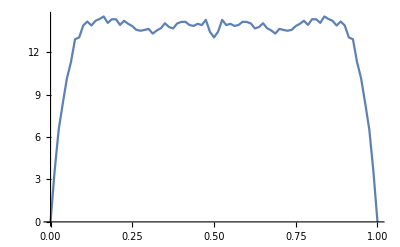

```mathematica
Show[datPlot]
```

```mathematica
yy
```

{0.,0.239,0.469,0.651,0.834,0.951,1.086,1.18,1.293,1.41,1.511,1.559,1.654,1.68,1.74,1.71,1.699,1.674,1.674,1.735,1.737,1.731,1.713,1.726,1.698,1.725,1.711,1.763,1.784,1.779,1.787,1.815,1.83,1.838,1.885,1.882,1.939,1.864,1.889,1.891,1.88,1.848,1.867,1.794,1.769,1.734,1.739,1.801,1.769,1.828,1.847,1.874,1.837,1.94,1.961,1.907,1.852,1.872,1.876,1.923,1.891,1.866,1.789,1.768,1.692,1.677,1.707,1.627,1.604,1.535,1.484,1.486,1.39,1.304,1.153,0.955,0.853,0.707,0.492,0.246,0.}

```mathematica
gLst
```

PythonError

```mathematica
2gLst⟦1⟧xCoords(1-xCoords)
```

{0.,0.284968,0.562721,0.83326,1.09659,1.3527,1.60159,1.84327,2.07774,2.30499,2.52503,2.73786,2.94346,3.14186,3.33304,3.51701,3.69376,3.8633,4.02562,4.18073,4.32863,4.46931,4.60277,4.72902,4.84806,4.95988,5.06449,5.16189,5.25207,5.33503,5.41078,5.47932,5.54064,5.59475,5.64164,5.68132,5.71379,5.73904,5.75707,5.76789,5.7715,5.76789,5.75707,5.73904,5.71379,5.68132,5.64164,5.59475,5.54064,5.47932,5.41078,5.33503,5.25206,5.16189,5.06449,4.95988,4.84806,4.72902,4.60277,4.46931,4.32863,4.18073,4.02562,3.8633,3.69376,3.51701,3.33304,3.14186,2.94346,2.73786,2.52503,2.30499,2.07774,1.84327,1.60159,1.3527,1.09659,0.83326,0.562721,0.284968,0.}

```mathematica
gLst
```

{11.553,32.125,47.221,56.982,61.863,61.863,56.982,47.221,32.125,11.553}

```mathematica
?MaTeX
```

```mathematica
fileNameGlst
```

gLst_N_20_param_divide_[80, 20, 20]_instanceNum_1000_seed_1000.npy

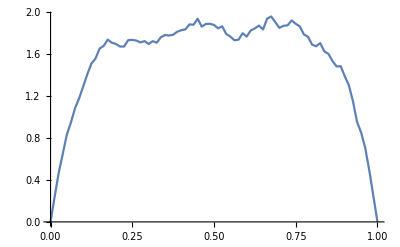

```mathematica
datPlot
```

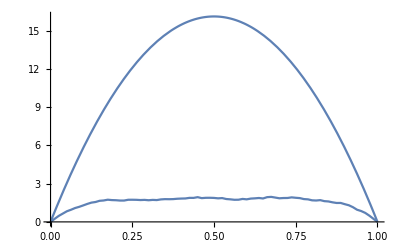

```mathematica
Show[uncorrPlot,datPlot]
```

```mathematica
ListLinePlot[Transpose@{xCoords,yy}]
```

-Graphics-

```mathematica
nameAppend[fileName,fileNameMod]
```

deltaN_N_10_param_divide_[80 16 16]_instanceNum_1000_seed_1000_threadedMKLtest.npy_threadedMKLtest

```mathematica
fileName
```

deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy

```mathematica
""==""
```

True

```mathematica
ArrToStrPy[paramDiv]
```

[, 80, 16, 16]

```mathematica
Py[fileName]
```

"deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy"

```mathematica
ExternalEvaluate["Python",
"import os
print(os.getcwd())"]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules

```mathematica
fileNameTest="deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy";
```

```mathematica
Py[fileNameTest]
```

"deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy"

```mathematica
Py[Directory[]]
```

"D:\\Ohdraw.niL\\Google_drive\\Programming\\Julia\\Modules"

```mathematica
Py[Directory[]]<>Py[fileNameTest]
```

"D:\\Ohdraw.niL\\Google_drive\\Programming\\Julia\\Modules""deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy"

```mathematica
"\\\\"
```

\\

```mathematica
Py[Directory[]<>"\\\\"<>fileNameTest]
```

"D:\\Ohdraw.niL\\Google_drive\\Programming\\Julia\\Modules\\\\deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy"

```mathematica
deltaNLst=Normal[ExternalEvaluate[sessPy,
"import numpy as np
np.load("<>Py[Directory[]<>"\\\\"<>fileNameTest]<>")"]];
```

```mathematica
deltaNLst⟦10,-1⟧
```

0.

```mathematica
{deltaNLst⟦1,-1⟧}~Join~deltaNLst⟦1⟧
```

{0.,0.242,0.471,0.672,0.859,1.004,1.139,1.233,1.271,1.374,1.483,1.592,1.599,1.664,1.671,1.613,1.63,1.7,1.748,1.841,1.791,1.862,1.797,1.854,1.852,1.839,1.847,1.843,1.884,1.849,1.822,1.92,1.92,1.882,1.885,1.795,1.795,1.839,1.844,1.83,1.88,1.889,1.843,1.921,1.892,1.903,1.838,1.858,1.845,1.84,1.933,1.863,1.958,1.902,1.922,1.918,1.911,1.85,1.85,1.883,1.843,1.815,1.785,1.8,1.71,1.673,1.649,1.603,1.588,1.551,1.505,1.381,1.288,1.224,1.111,0.994,0.851,0.676,0.523,0.295,0.}

```mathematica
xCoords=1/div Table[x,{x,0,div}];
```

```mathematica
xCoords
```

{0,1/80,1/40,3/80,1/20,1/16,3/40,7/80,1/10,9/80,1/8,11/80,3/20,13/80,7/40,3/16,1/5,17/80,9/40,19/80,1/4,21/80,11/40,23/80,3/10,5/16,13/40,27/80,7/20,29/80,3/8,31/80,2/5,33/80,17/40,7/16,9/20,37/80,19/40,39/80,1/2,41/80,21/40,43/80,11/20,9/16,23/40,47/80,3/5,49/80,5/8,51/80,13/20,53/80,27/40,11/16,7/10,57/80,29/40,59/80,3/4,61/80,31/40,63/80,4/5,13/16,33/40,67/80,17/20,69/80,7/8,71/80,9/10,73/80,37/40,15/16,19/20,77/80,39/40,79/80,1}

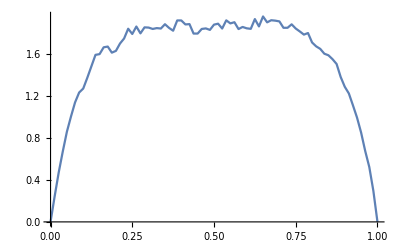

```mathematica
fig=ListLinePlot[Transpose@{xCoords,{deltaNLst⟦1,-1⟧}~Join~deltaNLst⟦1⟧}]
```

```mathematica
Head[fig]
```

Graphics

```mathematica
Normal[deltaNLst]
```

{{0.242,0.471,0.672,0.859,1.004,1.139,1.233,1.271,1.374,1.483,1.592,1.599,1.664,1.671,1.613,1.63,1.7,1.748,1.841,1.791,1.862,1.797,1.854,1.852,1.839,1.847,1.843,1.884,1.849,1.822,1.92,1.92,1.882,1.885,1.795,1.795,1.839,1.844,1.83,1.88,1.889,1.843,1.921,1.892,1.903,1.838,1.858,1.845,1.84,1.933,1.863,1.958,1.902,1.922,1.918,1.911,1.85,1.85,1.883,1.843,1.815,1.785,1.8,1.71,1.673,1.649,1.603,1.588,1.551,1.505,1.381,1.288,1.224,1.111,0.994,0.851,0.676,0.523,0.295,0.},{0.71,1.355,1.839,2.34,2.783,3.099,3.249,3.341,3.522,3.669,3.838,3.951,4.004,4.135,4.161,4.236,4.444,4.315,4.512,4.396,4.486,4.454,4.799,4.833,4.692,4.62,4.689,4.781,4.615,4.58,4.603,4.545,4.427,4.319,4.159,4.382,4.522,4.408,4.39,4.52,4.486,4.455,4.537,4.637,4.488,4.48,4.652,4.576,4.502,4.562,4.392,4.383,4.476,4.486,4.389,4.347,4.528,4.393,4.51,4.473,4.527,4.517,4.458,4.367,4.302,4.335,4.194,4.241,4.096,3.933,3.803,3.49,3.216,2.841,2.515,2.25,1.911,1.346,0.756,0.001},{1.071,2.011,2.58,3.22,3.637,4.234,4.528,4.61,4.969,5.107,5.12,5.171,5.191,5.556,5.669,5.758,5.899,5.779,5.685,5.928,6.025,5.974,5.922,5.772,5.858,5.62,5.752,5.885,5.802,5.704,5.742,5.902,5.779,5.671,5.704,5.835,5.83,5.595,5.638,5.673,5.769,5.585,5.566,5.891,5.74,5.67,5.464,5.314,5.547,5.601,5.914,5.992,5.752,5.966,6.214,6.303,6.236,6.034,6.369,6.169,6.199,6.054,5.902,5.846,5.488,5.647,5.48,5.262,5.225,5.184,5.064,4.894,4.565,4.36,3.846,3.287,2.69,1.835,1.032,0.},{1.113,2.205,2.971,3.822,4.523,5.061,5.538,5.628,5.738,5.766,6.096,6.252,6.207,6.144,6.365,6.44,6.526,6.404,6.531,6.625,6.593,6.797,6.894,6.577,6.674,6.599,6.458,6.413,6.491,6.604,6.701,6.641,6.453,6.651,6.762,6.506,6.683,6.769,6.542,6.295,6.315,6.223,6.389,6.701,6.935,6.685,6.655,6.555,6.634,6.527,6.735,6.837,6.859,6.892,7.071,6.943,6.851,6.883,6.701,6.743,6.737,6.918,7.071,6.941,6.856,6.54,6.504,6.699,6.477,6.268,6.126,5.956,5.406,5.219,4.643,3.906,3.148,2.484,1.301,0.001},{1.32,2.322,3.253,3.973,4.658,5.253,5.623,5.779,5.742,6.359,6.767,7.063,7.159,6.991,7.349,7.394,7.314,7.11,7.143,7.219,7.185,7.453,7.639,7.249,7.323,6.768,6.879,6.817,6.859,6.751,6.783,6.741,6.938,7.078,7.753,8.303,8.566,9.256,9.865,10.513,10.278,9.674,9.117,8.67,8.52,8.338,7.957,7.942,7.793,7.829,7.387,7.451,7.402,7.364,7.485,7.4,7.393,7.321,7.198,7.213,6.942,6.859,7.185,7.109,6.95,6.944,7.14,7.432,7.241,6.957,6.622,6.58,5.865,5.476,4.912,4.185,3.616,2.658,1.374,0.},{1.217,2.367,3.336,4.245,5.023,5.543,5.774,5.797,6.366,6.404,6.59,6.748,6.807,6.935,7.324,7.221,7.13,6.816,7.019,7.04,7.001,6.976,7.438,7.192,7.273,6.763,7.199,7.285,7.288,7.072,7.229,7.375,7.438,7.769,7.985,8.324,8.587,9.025,9.559,10.513,9.979,9.815,9.342,8.73,8.413,8.144,7.876,7.64,7.441,7.16,6.908,7.242,7.32,7.244,7.216,7.183,6.805,7.001,6.904,6.922,6.742,6.752,6.978,6.962,6.844,6.891,6.912,6.93,6.792,6.596,6.504,6.112,5.805,5.287,5.21,4.364,3.507,2.565,1.342,0.},{1.328,2.414,3.21,4.064,4.834,5.072,5.21,5.588,5.911,5.836,5.864,6.112,6.07,6.191,6.358,6.472,6.774,6.84,6.688,6.768,7.012,7.273,7.074,6.996,6.881,6.539,6.675,6.724,6.63,6.549,6.181,6.213,6.127,6.412,6.43,6.425,6.479,6.433,6.152,6.298,6.503,6.673,6.857,6.766,6.789,6.851,6.996,6.744,6.28,6.192,6.458,6.78,6.663,6.532,6.711,6.49,6.406,6.366,6.539,6.601,6.629,6.539,6.544,6.249,6.218,6.079,6.028,5.859,5.749,5.93,5.565,5.465,4.959,5.033,4.752,3.882,3.145,2.305,1.31,0.001},{1.018,1.898,2.521,3.342,3.819,4.265,4.397,4.799,5.244,5.468,5.693,5.711,5.561,5.749,6.099,6.104,6.119,6.037,6.222,6.138,6.286,6.155,5.807,5.981,5.797,5.776,5.823,5.599,5.866,5.939,5.995,6.095,6.252,6.289,5.991,5.904,6.037,5.832,5.699,5.673,5.75,5.846,5.861,5.865,5.764,6.103,6.267,6.057,5.79,5.982,6.097,6.028,5.916,6.105,6.074,6.223,5.982,5.904,5.942,6.301,6.378,6.229,6.085,5.989,5.879,5.631,5.661,5.54,5.347,5.137,4.993,4.857,4.316,3.936,3.645,3.3,2.607,1.784,1.099,0.},{0.634,1.189,1.603,2.269,2.55,2.906,3.204,3.602,3.788,3.836,4.026,4.165,4.366,4.436,4.293,4.255,4.384,4.263,4.292,4.261,4.303,4.265,4.386,4.365,4.474,4.349,4.474,4.625,4.588,4.623,4.713,4.696,4.62,4.655,4.665,4.616,4.623,4.554,4.544,4.517,4.725,4.624,4.518,4.493,4.314,4.316,4.398,4.456,4.479,4.55,4.649,4.596,4.735,4.702,4.768,4.789,5.001,4.646,4.913,4.807,4.823,4.697,4.792,4.656,4.403,4.369,4.418,4.242,4.014,3.829,3.642,3.55,3.194,2.93,2.598,2.221,1.817,1.261,0.701,0.001},{0.239,0.469,0.651,0.834,0.951,1.086,1.18,1.293,1.41,1.511,1.559,1.654,1.68,1.74,1.71,1.699,1.674,1.674,1.735,1.737,1.731,1.713,1.726,1.698,1.725,1.711,1.763,1.784,1.779,1.787,1.815,1.83,1.838,1.885,1.882,1.939,1.864,1.889,1.891,1.88,1.848,1.867,1.794,1.769,1.734,1.739,1.801,1.769,1.828,1.847,1.874,1.837,1.94,1.961,1.907,1.852,1.872,1.876,1.923,1.891,1.866,1.789,1.768,1.692,1.677,1.707,1.627,1.604,1.535,1.484,1.486,1.39,1.304,1.153,0.955,0.853,0.707,0.492,0.246,0.}}

```mathematica
Directory[]
```

D:\Ohdraw.niL\Documents

```mathematica
NotebookDirectory[]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules\

```mathematica
deltaNLst
```

Failure[…]

```mathematica
ExternalEvaluate["Python",
<|"Command"->"numpy.load","Arguments"->{"Py[fileName]"}|>]
```

Failure[…]

```mathematica
FindExternalEvaluators[]
```

```mathematica
ToString[Mlst]
```

{10}

```mathematica
"["<>StringTrim@StringJoin[" "<>ToString[#,InputForm]&/@paramDiv]<>"]"
```

[80 16 16]

```mathematica
Row[ToString[#, InputForm] & /@ paramDim, "  "]
```

StringJoin::string: String expected at position 2 in [<>  .

[<>    801616

```mathematica
Head[test]
```

String

```mathematica
"["<>(Row[ToString[#, InputForm] & /@ paramDim, "  "])<>"]"
```

StringJoin::string: String expected at position 2 in [<>  <>].

[<>    801616<>]

```mathematica
"M"<>"_"
```

M_

```mathematica
M
```

10

```mathematica
ExternalEvaluate["Python",
"import numpy as np
x = np.arange(10)
x"]
```

NumericArray[…]

```mathematica
Normal[%]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
RegisterExternalEvaluator["Python","C:\\ProgramData\\Anaconda3\\python.exe"]
```

49144367-4428-4e2c-bce2-77e66f775641

```mathematica
FindExternalEvaluators["Python"]
```

```mathematica
Head[Directory[]]
```

String

## Obsolete

```mathematica
xyLabs=MaTeX[#,Magnification->1]&/@{"k_3 / 2\\pi","\\left( \\Delta \\textstyle{\\sum}_{n=1}^m C_n \\right)^2"};
```